## Ver2 (nx x ny data in two columns)

```mathematica
$Version
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];(*Mathematica file in the proper location*)
filename=FileBaseName[NotebookFileName[]];
```

12.3.0 for Mac OS X x86 (64-bit) (May 10, 2021)

-Graphics-

### a. Data import and function def.

#### 0. Data information

```mathematica
Lx=1000;(*um-scanned area *)
Ly=100;(*um-scanned area *)
dx=5;(*step distance*)
dy=20;(*step distance*)
nx=Lx/dx+1;(*sample per line*)
ny=Ly/dy+1;(*sample per line*)
```

#### 1. Data import

```mathematica
allFiles=FileNames["*.txt"];
```

```mathematica
Print["Imported file names: ",allFiles]
allData=Import[#,"Data"]&/@allFiles;
allData//Dimensions
ndataset=Length[allFiles]
labels=FileBaseName/@allFiles
```

Imported file names: {as12.txt,as13.txt}

{2,1228}

2

{as12,as13}

#### 2. Data process &

```mathematica
cleaning[data_]:=Module[{start,drop1,dt},
start=FirstPosition[data,s_/;StringContainsQ[ToString[s],"Point Cloud:"]];
drop1=Drop[data,start[[1]]+1];
If[StringMatchQ[ToString[drop1[[1]]],"X\tY\tZ"],drop1=Rest[drop1],"error: no XYZ identified"];
dt=Interpreter["Number"]/@StringSplit[#,"\t"]&/@drop1;(*function &/@ list -> & means "this is a function." *)
dt];
```

```mathematica
StringSplit["x y z"](*any space and tabs*)
StringSplit["x y z","\t"](*only tabs*)
StringSplit["x x2\ty\tz","\t"](*only tabs*)
```

{x,y,z}

{x y z}

{x x2,y,z}

```mathematica
Interpreter["Number"]/@{"0","50","1.23e-11"}
%[[3]]*10^9
```

{0,50,1.23×10^-11}

0.0123

```mathematica
cleanedData=cleaning/@allData;
cleanedData//Dimensions
```

{2,1206,3}

```mathematica
zMat=ArrayReshape[#*10^9,{ny,nx}]&/@(#[[All,3]]&/@cleanedData);
zMat//Dimensions
zMat[[1]]//Dimensions
zMat[[1]]//MatrixForm
```

{2,6,201}

{6,201}

(0.0173718 | 0.0205303 | 0.00473778 | 0.0205303 | 0.0236889 | 0.00473778 | -0.000315837 | 0.00473778 | 0.0110548 | 0.0287425 | 0.0293742 | 0.0236889 | 0.00663289 | 0.008528 | 0.0281108 | -0.000315837 | -0.00284265 | -0.00347435 | 0.00410608 | -0.00410605 | -0.000947538 | 0.0243206 | 0.00789629 | 0.00410608 | 0.00600119 | 0.0142133 | 0.0356912 | 0.0161084 | 0.0198986 | -0.00600116 | -0.000315837 | -0.00347435 | -0.00852797 | 0.0154767 | 0.00473778 | 0.008528 | 0.0116865 | 0.00473778 | -0.00410605 | 0.0268474 | 0.0154767 | 0.0167401 | -0.000315837 | 0.0142133 | 0.0173718 | -0.000947538 | -0.00726456 | 0.000315865 | 0.0173718 | 0.00600119 | 0.00157927 | 0.0356912 | -0.000315837 | 0.00663289 | 0.0268474 | 0.025584 | 0.0091597 | 0.025584 | 0.0350595 | 0.00347438 | 0.0407448 | 0.0123182 | 0.0344278 | 0.008528 | 0.0142133 | 0.0123182 | 0.0337961 | 0.0647495 | 0.0862274 | 0.0780153 | 0.0546423 | 0.0565374 | 0.0660129 | 0.0622227 | 0.0559057 | 0.0729616 | 0.0837006 | 0.100125 | 0.114022 | 0.119076 | 0.136764 | 0.16519 | 0.173402 | 0.196775 | 0.19867 | 0.206251 | 0.214463 | 0.239099 | 0.215726 | 0.241626 | 0.262472 | 0.234046 | 0.261841 | 0.282055 | 0.271316 | 0.310482 | 0.322484 | 0.345225 | 0.356596 | 0.355964 | 0.340803 | 0.319957 | 0.309218 | 0.319957 | 0.280792 | 0.279528 | 0.291531 | 0.304796 | 0.333855 | 0.33575 | 0.33575 | 0.367967 | 0.337645 | 0.299743 | 0.269421 | 0.249207 | 0.241626 | 0.274475 | 0.275106 | 0.296584 | 0.350911 | 0.375547 | 0.388181 | 0.438717 | 0.431769 | 0.426715 | 0.450088 | 0.451351 | 0.39513 | 0.386286 | 0.385654 | 0.486095 | 0.520838 | 0.477883 | 0.461459 | 0.524629 | 0.496202 | 0.489254 | 0.536631 | 0.494939 | 0.431769 | 0.834163 | 0.619384 | 0.469039 | 0.33954 | 0.258682 | 0.263736 | 0.403974 | 1.65348 | 1.83857 | 2.23149 | 2.72864 | 2.92762 | 2.62125 | 2.31108 | 2.692 | 3.43109 | 20.7132 | 20.7132 | 20.7006 | 20.7132 | 20.686 | 20.6879 | 20.7132 | 20.6917 | 20.686 | 11.2326 | 5.66858 | 2.92826 | 1.69012 | 1.1178 | 0.848061 | 0.559372 | 0.448193 | 0.427347 | 0.376811 | 0.367335 | 0.396393 | 0.389444 | 0.379337 | 0.355964 | 0.370493 | 0.39892 | 0.397025 | 0.364176 | 0.354069 | 0.355964 | 0.367967 | 0.355964 | 0.363545 | 0.366071 | 0.388181 | 0.417871 | 0.656023 | 0.933341 | 1.05336 | 1.09821 | 1.02494 | 0.87775 | 0.611804 | 0.54737
0.00473778 | 0.0154767 | 0.00473778 | 0.0205303 | -0.00347435 | 0.0154767 | 0.0142133 | 0.00600119 | 0.0192669 | 0.00221097 | 0.0167401 | 0.0135816 | -0.00789627 | -0.000315837 | 0.00284268 | -0.00600116 | 0.0154767 | 0.0154767 | 0.0142133 | 0.0154767 | 0.0116865 | 0.0217937 | -0.00789627 | -0.0142133 | 0.00663289 | 0.00663289 | 0.00663289 | 0.0180035 | 0.00410608 | 0.0180035 | 0.00284268 | -0.0110548 | 0.000947568 | 0.0167401 | 0.00473778 | 0.0116865 | 0.0091597 | -0.00410605 | 0.0135816 | 0.0123182 | 0.0198986 | -0.00473775 | -0.0135816 | 0.00536948 | -0.0161084 | -0.00979137 | 0.021162 | 0.00410608 | 0.0091597 | -0.0110548 | 0.00600119 | 0.0205303 | 0.0243206 | 0.0110548 | -0.00536946 | 0.0344278 | 0.0312693 | 0.0154767 | 0.0167401 | 0.0243206 | 0.025584 | 0.0521155 | 0.0571691 | 0.0931761 | 0.108969 | 0.0874908 | 0.105178 | 0.0799104 | 0.0855957 | 0.100757 | 0.129815 | 0.128551 | 0.12792 | 0.136764 | 0.133605 | 0.145607 | 0.178456 | 0.19867 | 0.211304 | 0.199302 | 0.207514 | 0.214463 | 0.227097 | 0.232151 | 0.268789 | 0.242258 | 0.244153 | 0.241626 | 0.246048 | 0.273843 | 0.294689 | 0.278265 | 0.278897 | 0.298479 | 0.314272 | 0.346489 | 0.360386 | 0.325643 | 0.325643 | 0.340172 | 0.340803 | 0.350911 | 0.352806 | 0.367967 | 0.385023 | 0.398288 | 0.551792 | 0.529051 | 0.488622 | 0.477251 | 0.568848 | 0.533473 | 0.475356 | 0.386286 | 0.334486 | 0.298479 | 0.261841 | 0.307323 | 0.31364 | 0.345857 | 0.380601 | 0.373652 | 0.350911 | 0.318062 | 0.278265 | 0.319326 | 0.354069 | 0.332591 | 0.332591 | 0.323116 | 0.331328 | 0.337645 | 0.316799 | 0.328169 | 0.307323 | 0.287109 | 0.258682 | 0.229624 | 0.209409 | 0.200566 | 0.193617 | 0.201197 | 0.201197 | 0.195512 | 0.192985 | 0.196775 | 0.546107 | 1.36163 | 1.55304 | 2.09441 | 2.81076 | 3.87013 | 4.89222 | 5.03435 | 4.53847 | 4.32748 | 5.05014 | 5.89536 | 20.7132 | 20.6898 | 20.7132 | 20.7132 | 20.6879 | 20.7132 | 20.6886 | 15.6375 | 8.76203 | 4.75577 | 2.62693 | 1.5025 | 0.849324 | 0.565058 | 0.464617 | 0.421661 | 0.337645 | 0.374915 | 0.380601 | 0.335118 | 0.319326 | 0.294057 | 0.327538 | 0.346489 | 0.371125 | 0.370493 | 0.36923 | 0.413449 | 0.48799 | 0.554319 | 0.676869 | 0.926392 | 0.89607 | 0.868275 | 0.74762 | 0.572638 | 0.714771 | 1.3509 | 1.75582 | 1.6598 | 1.90111 | 1.77793 | 1.47345
0.00410608 | 0.00157927 | 0.00157927 | 0.0420082 | 0.00221097 | 0.0268474 | 0.014845 | 0.0281108 | 0.000947568 | 0.0268474 | 0.0224254 | 0.000315865 | 0.0243206 | 0.00600119 | 0.0337961 | -0.00473775 | -0.00663286 | 0.008528 | 0.0262157 | 0.0198986 | 0.0224254 | 0.0104231 | 0.0180035 | 0.0243206 | 0.0205303 | 0.0192669 | 0.0167401 | 0.0268474 | 0.014845 | 0.014845 | 0.0167401 | -0.000947538 | 0.0224254 | -0.00284265 | -0.00284265 | 0.031901 | -0.00410605 | 0.0192669 | 0.0325327 | 0.00473778 | 0.0173718 | 0.000315865 | 0.0192669 | 0.0135816 | -0.000947538 | -0.000947538 | 0.0356912 | 0.00726459 | 0.0167401 | 0.0293742 | 0.0180035 | 0.0274791 | 0.0394814 | 0.0420082 | 0.0439033 | 0.0394814 | 0.0375863 | 0.0476935 | 0.0672763 | 0.074225 | 0.0622227 | 0.0666446 | 0.0900176 | 0.108969 | 0.107705 | 0.150661 | 0.149398 | 0.146871 | 0.145607 | 0.141817 | 0.1614 | 0.16519 | 0.16519 | 0.179088 | 0.19867 | 0.201829 | 0.206251 | 0.210673 | 0.207514 | 0.225834 | 0.24289 | 0.249207 | 0.252997 | 0.262472 | 0.263736 | 0.27258 | 0.268158 | 0.267526 | 0.278897 | 0.309218 | 0.33575 | 0.350279 | 0.359755 | 0.361018 | 0.382496 | 0.446298 | 0.434927 | 0.433032 | 0.446298 | 0.445034 | 0.453246 | 0.473461 | 0.524629 | 0.544212 | 0.582746 | 0.572638 | 0.568216 | 0.57327 | 0.564426 | 0.603592 | 0.63265 | 0.613699 | 0.628228 | 0.566953 | 0.565058 | 0.530946 | 0.565058 | 0.599801 | 0.611172 | 0.577692 | 0.597906 | 0.586536 | 0.585272 | 0.597906 | 0.585272 | 0.562531 | 0.540421 | 0.502519 | 0.489254 | 0.441876 | 0.380601 | 0.364808 | 0.36544 | 0.344594 | 0.337013 | 0.328169 | 0.352806 | 0.373652 | 0.360386 | 0.327538 | 0.31364 | 0.286477 | 0.293426 | 0.296584 | 0.315535 | 0.278897 | 0.270053 | 0.28395 | 0.374915 | 0.698979 | 1.35784 | 2.03882 | 2.81013 | 3.2201 | 3.26116 | 2.82023 | 3.00406 | 3.10387 | 2.67747 | 2.8613 | 6.20932 | 20.7132 | 20.7132 | 20.693 | 20.6785 | 19.2571 | 11.683 | 6.93514 | 3.76337 | 2.15126 | 1.22835 | 0.715403 | 0.461459 | 0.337013 | 0.292162 | 0.306692 | 0.304796 | 0.30985 | 0.318694 | 0.380601 | 0.410291 | 0.412817 | 0.400815 | 0.409659 | 0.411554 | 0.464617 | 0.587799 | 0.744461 | 0.822161 | 1.0142 | 1.07295 | 0.84427 | 0.698979 | 0.583377 | 0.513258 | 0.453878 | 0.561267 | 0.775415 | 0.885331 | 0.837953 | 0.748252
0.0243206 | 0.0167401 | 0.0192669 | 0.00284268 | 0.0407448 | 0.0091597 | 0.000947568 | -0.0104231 | -0.000947538 | -0.00915967 | -0.00347435 | 0.00663289 | 0.0142133 | 0.00726459 | 0.0205303 | 0.0287425 | 0.0167401 | 0.00536948 | 0.0123182 | 0.0104231 | 0.00347438 | 0.0198986 | 0.0142133 | -0.0198986 | 0.0110548 | 0.0123182 | -0.00347435 | 0.0142133 | -0.00473775 | 0.0116865 | -0.0116865 | 0.0091597 | 0.00410608 | 0.0262157 | 0.00284268 | -0.00410605 | 0.0154767 | -0.000315837 | -0.000315837 | 0.0110548 | 0.008528 | 0.0091597 | 0.0135816 | 0.00157927 | 0.00221097 | 0.0192669 | 0.0154767 | 0.0116865 | -0.00284265 | 0.00726459 | 0.0123182 | 0.00473778 | 0.025584 | 0.0356912 | 0.0312693 | 0.021162 | 0.0344278 | 0.0457984 | 0.0508521 | 0.0672763 | 0.0698031 | 0.0982298 | 0.097598 | 0.123498 | 0.128551 | 0.142449 | 0.160768 | 0.148134 | 0.178456 | 0.192985 | 0.210673 | 0.233414 | 0.243521 | 0.230887 | 0.234046 | 0.237204 | 0.273211 | 0.307323 | 0.327538 | 0.314272 | 0.312377 | 0.313009 | 0.312377 | 0.274475 | 0.269421 | 0.288372 | 0.301006 | 0.326906 | 0.34712 | 0.376179 | 0.36165 | 0.401447 | 0.410922 | 0.443771 | 0.466512 | 0.479778 | 0.482305 | 0.4583 | 0.511995 | 0.594748 | 0.618121 | 0.603592 | 0.606118 | 0.561267 | 0.553055 | 0.553687 | 0.563163 | 0.538526 | 0.594748 | 0.625701 | 0.886594 | 0.762781 | 0.608645 | 0.558109 | 0.544212 | 0.518312 | 0.506309 | 0.498097 | 0.4842 | 0.467144 | 0.458932 | 0.447561 | 0.431769 | 0.437454 | 0.461459 | 0.433032 | 0.481673 | 0.497466 | 0.477251 | 0.437454 | 0.39513 | 0.392603 | 0.376811 | 0.348384 | 0.345857 | 0.389444 | 0.323747 | 0.266894 | 0.215726 | 0.273843 | 0.366071 | 0.4583 | 0.49557 | 0.469671 | 0.362913 | 0.312377 | 0.285214 | 0.24668 | 0.245416 | 0.275738 | 0.565058 | 1.03631 | 1.79561 | 6.41462 | 5.095 | 4.89538 | 5.93958 | 7.69319 | 20.7132 | 20.6898 | 20.7126 | 20.7075 | 20.7132 | 20.693 | 20.7132 | 20.6905 | 20.4725 | 10.1612 | 5.50055 | 2.82718 | 1.41407 | 0.797524 | 0.524629 | 0.383127 | 0.299743 | 0.259314 | 0.248575 | 0.282055 | 0.367335 | 0.341435 | 0.329433 | 0.319957 | 0.355332 | 0.4583 | 0.487358 | 0.53979 | 0.522102 | 0.506309 | 0.650338 | 0.770361 | 0.750147 | 0.64023 | 0.542948 | 0.527156 | 0.537895 | 0.614962 | 0.789312 | 0.880909 | 0.927023 | 0.935236 | 0.740671
0.0205303 | -0.00663286 | 0.021162 | 0.025584 | -0.00410605 | 0.0123182 | 0.00410608 | 0.0205303 | 0.0154767 | -0.00536946 | -0.0104231 | 0.0306376 | 0.0167401 | -0.0161084 | -0.00473775 | 0.0192669 | 0.0274791 | 0.0217937 | 0.00726459 | 0.0142133 | -0.0198986 | 0.00726459 | 0.0167401 | -0.0116865 | -0.00347435 | 0.0123182 | -0.00979137 | 0.0097914 | 0.0097914 | 0.0142133 | -0.000947538 | 0.00473778 | 0.00726459 | 0.0161084 | 0.00663289 | 0.0142133 | -0.00852797 | 0.0192669 | 0.00726459 | 0.00600119 | 0.00410608 | 0.00536948 | 0.021162 | -0.000315837 | 0.00663289 | -0.00979137 | 0.0123182 | -0.00663286 | 0.0192669 | -0.0116865 | 0.0123182 | 0.00600119 | 0.0243206 | 0.0375863 | 0.0243206 | 0.0350595 | 0.0439033 | 0.0394814 | 0.0533789 | 0.0660129 | 0.0925444 | 0.104547 | 0.0957029 | 0.115286 | 0.132973 | 0.163927 | 0.163927 | 0.175297 | 0.182246 | 0.1873 | 0.201197 | 0.199302 | 0.22457 | 0.261841 | 0.279528 | 0.274475 | 0.325011 | 0.345857 | 0.337645 | 0.307955 | 0.304796 | 0.313009 | 0.325643 | 0.478514 | 0.468407 | 0.42861 | 0.403342 | 0.386286 | 0.390708 | 0.349015 | 0.343962 | 0.379969 | 0.409659 | 0.429242 | 0.451983 | 0.492412 | 0.467144 | 0.489254 | 0.489254 | 0.484832 | 0.535368 | 0.54737 | 0.544843 | 0.509468 | 0.5101 | 0.548002 | 0.561267 | 0.587167 | 0.57706 | 0.651601 | 0.711613 | 0.649074 | 0.56948 | 0.506309 | 0.49178 | 0.471566 | 0.471566 | 0.498097 | 0.54737 | 0.546107 | 0.524629 | 0.489254 | 0.537263 | 0.525892 | 0.554319 | 0.600433 | 0.579587 | 0.535999 | 0.474093 | 0.451351 | 0.412186 | 0.407132 | 0.380601 | 0.361018 | 0.344594 | 0.30227 | 0.292162 | 0.252997 | 0.234046 | 0.174666 | 0.145607 | 0.316167 | 0.244785 | 0.198039 | 0.225202 | 0.204356 | 0.172139 | 0.249207 | 6.3963 | 4.12028 | 2.99901 | 2.94342 | 2.28518 | 2.53344 | 3.63008 | 4.93138 | 5.98696 | 6.9023 | 8.37606 | 14.1858 | 20.6879 | 20.7132 | 20.7132 | 20.7132 | 20.4643 | 13.6154 | 7.76583 | 3.97057 | 2.49301 | 1.38185 | 0.831005 | 0.498729 | 0.447561 | 0.69203 | 0.836058 | 0.960504 | 1.33447 | 0.98135 | 0.696452 | 0.505678 | 0.378706 | 0.285214 | 0.267526 | 0.325011 | 0.358491 | 0.396393 | 0.614962 | 0.623806 | 0.60296 | 0.796893 | 0.81079 | 0.939026 | 0.852482 | 0.757727 | 0.781732 | 0.693294 | 0.656023 | 0.729932 | 0.675606 | 0.576428 | 0.489254
0.132973 | 0.0451667 | 0.00789629 | 0.0192669 | 0.00536948 | 0.0167401 | 0.00221097 | 0.00284268 | 0.0110548 | -0.0180035 | -0.00473775 | 0.00410608 | 0.00726459 | 0.00284268 | 0.00347438 | 0.008528 | -0.00600116 | 0.00789629 | 0.00536948 | 0.00410608 | 0.00410608 | -0.000315837 | -0.0129499 | -0.0142133 | -0.000947538 | 0.00726459 | 0.00473778 | 0.00789629 | 0.00726459 | 0.0116865 | -0.000947538 | -0.000947538 | 0.00284268 | 0.0116865 | 0.0198986 | 0.0224254 | -0.0154767 | -0.0142133 | -0.00789627 | 0.025584 | 0.00473778 | 0.0274791 | 0.0173718 | 0.0224254 | 0.0186352 | 0.031901 | 0.0439033 | 0.0502204 | 0.0641178 | 0.0805421 | 0.0900176 | 0.103283 | 0.120339 | 0.145607 | 0.134868 | 0.141186 | 0.134868 | 0.152556 | 0.148134 | 0.152556 | 0.16898 | 0.174666 | 0.162032 | 0.189195 | 0.184773 | 0.186036 | 0.182878 | 0.186036 | 0.166454 | 0.2132 | 0.206883 | 0.208146 | 0.189195 | 0.213831 | 0.281423 | 0.252365 | 0.289636 | 0.264367 | 0.253629 | 0.263104 | 0.28395 | 0.421661 | 0.4065 | 0.407764 | 0.358491 | 0.352806 | 0.318694 | 0.330696 | 0.312377 | 0.328801 | 0.307955 | 0.324379 | 0.350911 | 0.367335 | 0.389444 | 0.688871 | 0.829741 | 0.714771 | 0.535999 | 0.441244 | 0.442508 | 0.452615 | 0.434295 | 0.486727 | 0.470934 | 0.479778 | 0.511995 | 0.549897 | 0.546107 | 0.571375 | 0.592853 | 0.539158 | 0.481041 | 0.471566 | 0.474724 | 0.501887 | 0.558109 | 0.553055 | 0.481673 | 0.425451 | 0.391971 | 0.409027 | 0.415344 | 0.380601 | 0.376179 | 0.346489 | 0.329433 | 0.300375 | 0.27258 | 0.30985 | 0.285214 | 0.256155 | 0.218885 | 0.186036 | 0.158241 | 0.184773 | 0.179088 | 0.156346 | 0.141186 | 0.138659 | 0.123498 | 0.0963346 | 0.0862274 | 0.0704348 | 0.0508521 | 0.0470618 | 0.0432716 | 0.0514838 | 1.04894 | 1.69454 | 1.15633 | 1.10516 | 0.800683 | 0.8329 | 1.55557 | 2.30856 | 20.7132 | 20.7069 | 20.6924 | 20.6917 | 20.7132 | 20.6879 | 20.6841 | 20.7132 | 20.4984 | 12.2718 | 6.96673 | 3.8158 | 2.09883 | 1.1159 | 0.662972 | 0.425451 | 0.386918 | 0.366071 | 0.313009 | 0.27258 | 0.249207 | 0.249207 | 0.231519 | 0.242258 | 0.248575 | 0.239099 | 0.243521 | 0.291531 | 0.392603 | 0.463985 | 0.477251 | 0.492412 | 0.435559 | 0.409659 | 0.482936 | 0.704664 | 1.05526 | 1.06347 | 1.03125 | 0.931445 | 0.791207 | 0.653496 | 0.596011 | 0.494307 | 0.467144)

#### Contour plot_function

```mathematica
tickX=Table[{i,ToString[(i-1)*dx]},{i,1,nx,50}];
tickY=Table[{i,ToString[(i-1)*dy]},{i,1,ny}];
asratio=2;
```

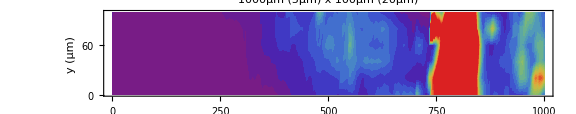

```mathematica
SetAttributes[mapB,HoldFirst];
mapB[temp_,min_,max_,dd_]:=Module[{leg},
leg=Round[Table[i,{i,min,max,(max-min)/dd}],0.001];
ListContourPlot[Evaluate[temp],PlotRange->All,Frame->True,ImageSize->Large,LabelStyle->{FontFamily->"Arial",FontSize->16,Black},
PlotLabel->Row[{Lx,"μm"," (",dx,"μm",") x ",Ly,"μm"," (",dy,"μm",")"}],
FrameLabel->{"x (μm)","y (μm)"},
FrameTicks->{{tickY,None},{tickX,None}},
AspectRatio->Ly/Lx*asratio,
GridLines->{Range[0,Lx,100],Range[0,Ly,10]*(ny-1)/Ly},
Method->{"GridLinesInFront"->True},ColorFunction->Function[{z},ColorData["Rainbow"][Rescale[z,{min,max}]]],ColorFunctionScaling->False,Contours->leg,ContourStyle->None,PlotLegends->Placed[BarLegend[{"Rainbow",{min,max}},LegendMarkerSize->Medium,LegendLabel->"Current (nA)"],{After,Top}]]];
mapB[zMat[[1]],0.1,2,20]
```

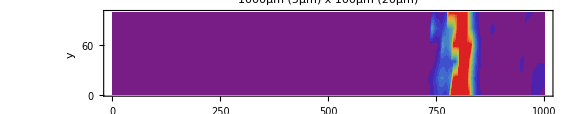

```mathematica
mapA1[temp_,cont_]:=Module[{},
ListContourPlot[temp,PlotRange->All,Frame->True,ImageSize->Large,LabelStyle->{FontFamily->"Arial",FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{tickY,None},{tickX,None}},
AspectRatio->Ly/Lx*asratio,
GridLines->{Range[0,Lx,100],Range[0,Ly,10]*(ny-1)/Ly},
Method->{"GridLinesInFront"->True},
ColorFunction->"Rainbow",Contours->cont,ContourStyle->None,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->Medium,LegendLabel->"Intensity"],{After,Top}],
PlotLabel->Row[{Lx,"μm"," (",dx,"μm",") x ",Ly,"μm"," (",dy,"μm",")"}]]]
mapA1[zMat[[1]],20]
```

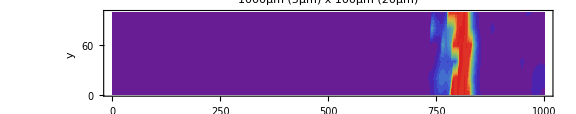

```mathematica
mapA2[temp_,cont_]:=Module[{rr},
rr=Round[Table[i,{i,Min[temp],Max[temp],(Max[temp]-Min[temp])/cont}],0.01];
ListContourPlot[temp,PlotRange->All,Frame->True,ImageSize->Large,LabelStyle->{FontFamily->"Arial",FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{tickY,None},{tickX,None}},
AspectRatio->Ly/Lx*asratio,
GridLines->{Range[0,Lx,100],Range[0,Ly,10]*(ny-1)/Ly},
Method->{"GridLinesInFront"->True},
ColorFunction->"Rainbow",Contours->rr,ContourStyle->None,
PlotLegends->Placed[BarLegend[{ColorData["Rainbow"],{Min[rr],Max[rr]}},LegendMarkerSize->Medium,LegendLabel->"Intensity"],{After,Top}],
PlotLabel->Row[{Lx,"μm"," (",dx,"μm",") x ",Ly,"μm"," (",dy,"μm",")"}]]]
mapA2[zMat[[1]],20]
```

#### Line profiles_function

```mathematica
ClearAll[LPy];
LPy[zMatn_,y_]:=Module[{rowIndex,xvals,lineProfile},
rowIndex=Round[y/dy]+1;
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatn[[rowIndex]];
ListLinePlot[Transpose[{xvals,lineProfile}],Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm  ",PlotRange->All,PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]];
```

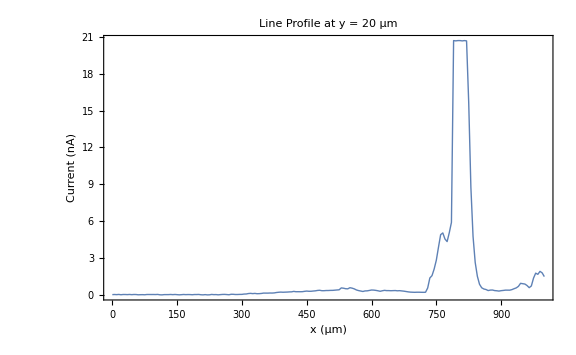

```mathematica
LPy[zMat[[1]],20]
```

#### Line profiles_comparison (need update)

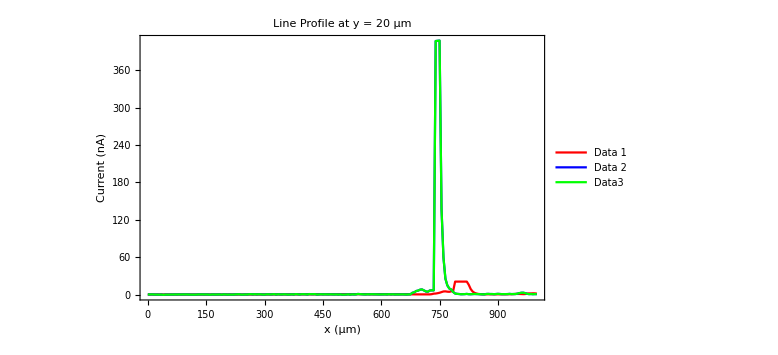

```mathematica
LPyCompare[z1_,z2_,z3_,y_]:=Module[{rowIndex,xvals,curve1,curve2,curve3},
rowIndex=Round[y/dy]+1;
xvals=Range[0,dx*(nx-1),dx];
curve1=Transpose[{xvals,z1[[rowIndex]]}];
curve2=Transpose[{xvals,z2[[rowIndex]]}];
curve3=Transpose[{xvals,z3[[rowIndex]]}];
ListLinePlot[{curve1,curve2,curve3},PlotStyle->{Red,Blue,Green},Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm",PlotRange->All,
PlotLegends->Placed[LineLegend[{"Data 1","Data 2","Data3"}],Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]];

LPyCompare[zMat[[1]],zMat[[2]],zMat[[2]],20]
```

#### Line profiles_avg

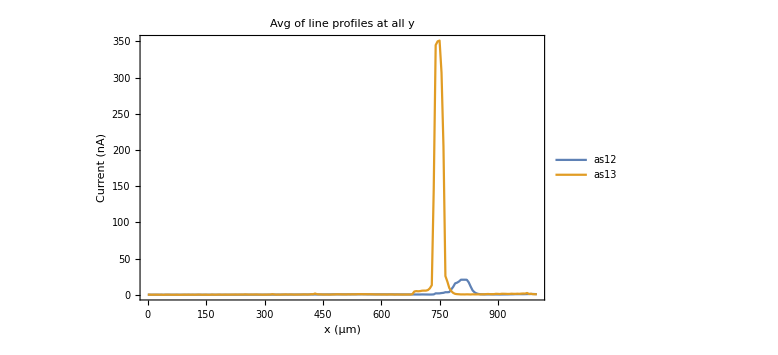

```mathematica
yIndices=Round[Range[0,Ly,dy]/dy]+1;
xvals=Range[0,dx*(nx-1),dx];
avgProf=Table[Thread[{xvals,Mean[zMat[[i,yIndices]]]}],{i,Length[zMat]}];
avgPplots=
ListLinePlot[Table[avgProf[[i]],{i,1,ndataset}],PlotStyle->Automatic,Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Avg of line profiles at all y",PlotRange->All,PlotLegends->Placed[LineLegend[labels],Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

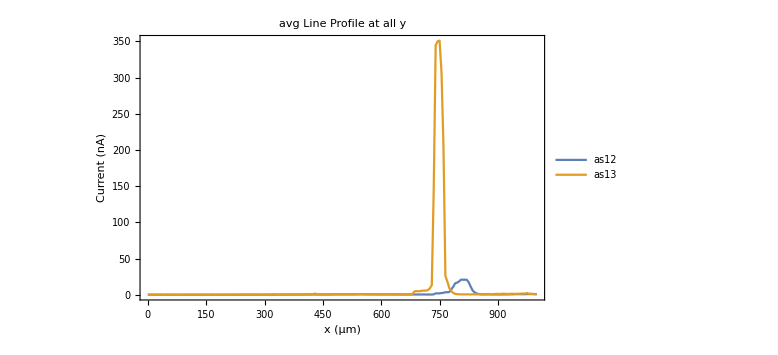

```mathematica
ListLinePlot[{avgProf[[1]],avgProf[[2]]},PlotStyle->Automatic,Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"avg Line Profile at all y",PlotRange->All,PlotLegends->Placed[{"as12","as13"},Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

## Check

-Graphics-

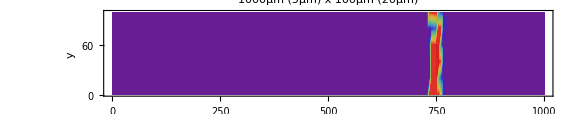

```mathematica
mapA2[zMat[[1]],20]
mapA2[zMat[[2]],20]
```

```mathematica
mapB[zMat[[1]],0.1,2,20]
```

-Graphics-

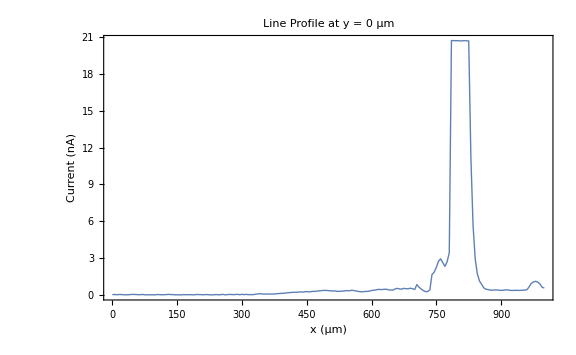
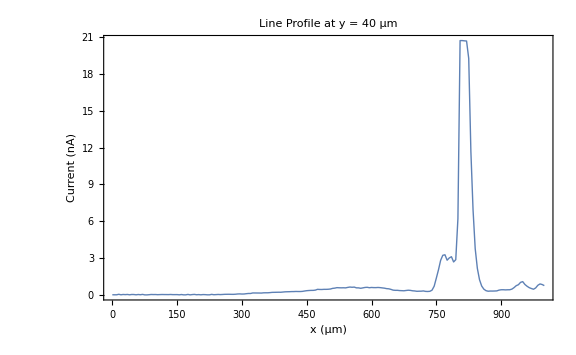
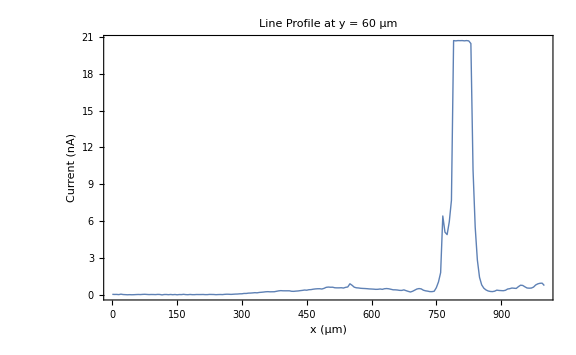
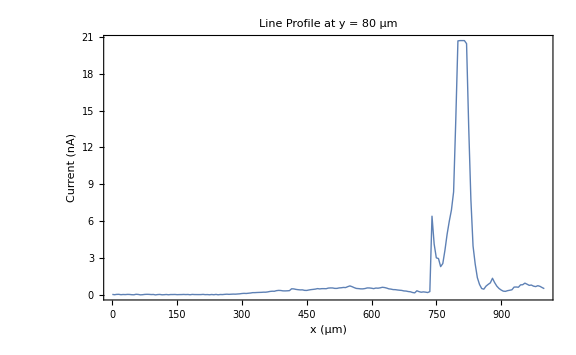
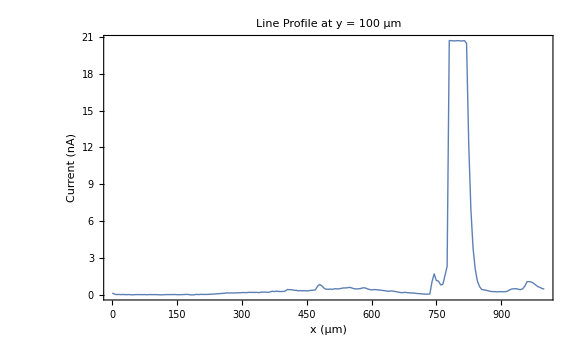
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[LPy[zMat[[1]],i],{i,0,100,20}]
```

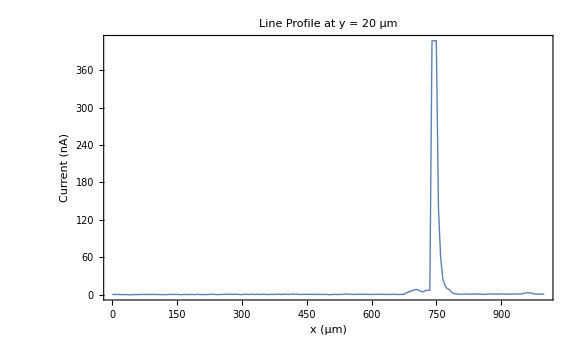
{-Graphics-,-Graphics-}

```mathematica
Table[LPy[zMat[[i]],20],{i,1,ndataset}]
```

```mathematica
avgPplots
```

-Graphics-

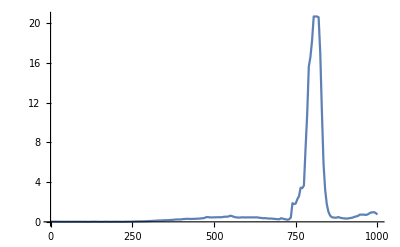

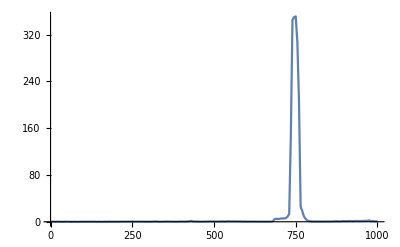

```mathematica
ListLinePlot[{avgProf[[1]]},PlotRange->Full,PlotLegends->labels[[1]]]
ListLinePlot[{avgProf[[2]]},PlotRange->Full,PlotLegends->labels[[2]]]
```

## Export

#### functions for data export and flip

```mathematica
flipXY[data_]:=MapThread[{#1[[1]],#2[[2]]}&,{data,Reverse[data]}];
```

```mathematica
flippedAvg=flipXY/@avgProfiles;
```

```mathematica
ListLinePlot[{flippedAvg[[1]],flippedAvg[[2]]},PlotStyle->Automatic,Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"avg Line Profile at all y",PlotRange->All,PlotLegends->Placed[{"as12","as13"},Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large];
```

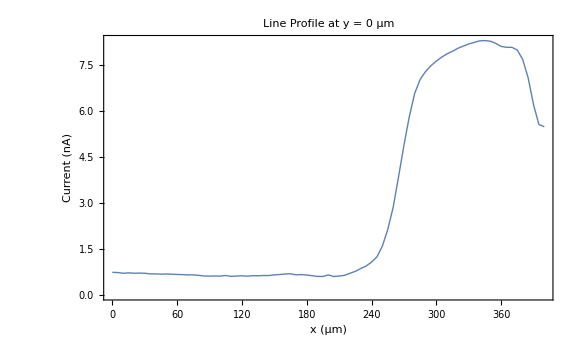

{81,2}

```mathematica
LPy[0]
data0=GetLPyRData[0];
data0//TableForm;
data0//Dimensions
```

```mathematica
t0=GetLPyRData[0];
t2=GetLPyRData[20];
t4=GetLPyRData[40];
t0//Dimensions
```

{81,2}

```mathematica
ttt={t0,t2,t4};
ttt//Dimensions
Export[filename<>"0-40.xlsx",ttt]
```

{3,81,2}

5_10_as0-40.xlsx

## --------later-----

#### Spike correction (need update, deactivated)

```mathematica
"ClearAll[getZ];
getZ[x_,y_]:=Module[{xi,yi},
xi=Round[x/dx]+1;
yi=Round[y/dy]+1;
];
```

```mathematica
"ClearAll[setZ];
setZ[x_,y_,newVal_]:=Module[{xi,yi},
xi=Round[x/dx]+1;
yi=Round[y/dy]+1;
];
```

```mathematica
"ClearAll[SmoothZSpike];
SmoothZSpike[xStart_,xEnd_,y_,noiseAmp_:0.05]:=Module[{xiStart,xiEnd,yi,z1,z2,n,xs,linFit,noise,newVals},(*Index conversion*)xiStart=Round[xStart/dx]+1;
xiEnd=Round[xEnd/dx]+1;
yi=Round[y/dy]+1;
(*Length and original endpoints*)
n=xiEnd-xiStart+1;
z1=zMatrix[[yi,xiStart]];
z2=zMatrix[[yi,xiEnd]];
(*X-index vector*)
xs=Range[0,n-1];
(*Linear interpolation+small noise*)
linFit=z1+(z2-z1)*(xs/(n-1));
noise=RandomReal[{-noiseAmp,noiseAmp},n];
newVals=linFit+noise;
(*Apply correction*)
Do[zMatrix[[yi,xiStart+i-1]]=newVals[[i]],{i,1,n}];
(*Return updated profile for review*)
newVals];
```

### b. Correction 1 (optional, need update)

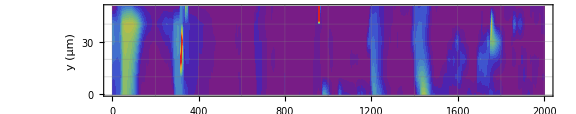

```mathematica
map[zMatrix,0.1,4,20]
```

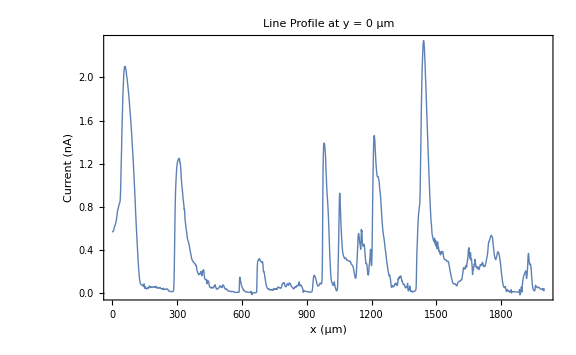

```mathematica
LPy[0]
```

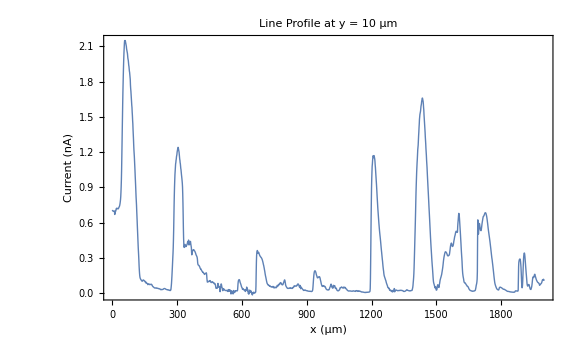

```mathematica
LPy[10]
```

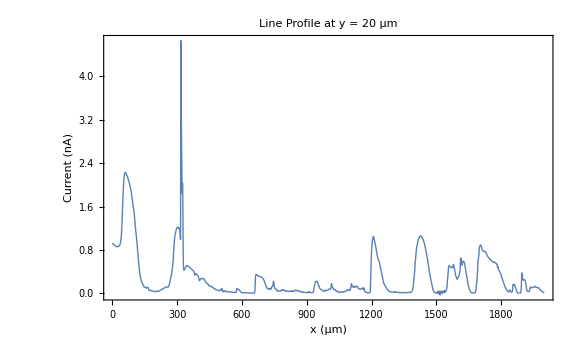

```mathematica
LPy[20]
```

```mathematica
Table[getZ[x,20],{x,310,340,1}]
```

{1.2,1.19,1.17,1.14,1.1,1.04,0.992,4.66,4.47,3.63,3.01,2.61,2.25,1.84,1.97,2.03,1.97,1.43,0.777,0.531,0.465,0.431,0.424,0.429,0.438,0.445,0.453,0.46,0.468,0.475,0.485}

```mathematica
Table[getZ[x,20],{x,316,328,1}]
```

{0.992,4.66,4.47,3.63,3.01,2.61,2.25,1.84,1.97,2.03,1.97,1.43,0.777}

```mathematica
SmoothZSpike[316,328,20]
```

{1.01926,1.01683,0.92821,0.968952,0.876188,0.904426,0.893926,0.91209,0.824584,0.867157,0.80053,0.750722,0.80336}

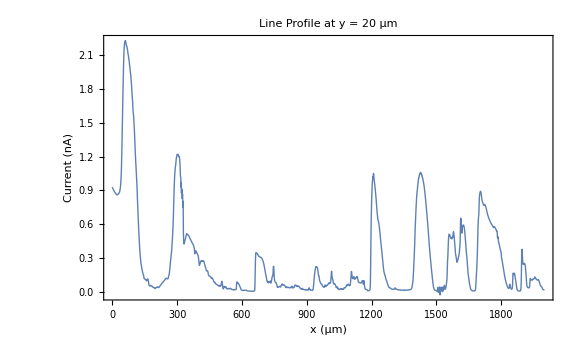

```mathematica
LPy[20]
```

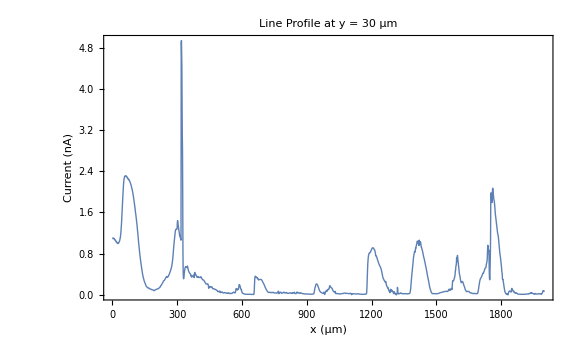

```mathematica
LPy[30]
```

```mathematica
Table[getZ[x,30],{x,300,340,1}]
```

{1.29,1.39,1.44,1.42,1.39,1.35,1.32,1.29,1.26,1.23,1.2,1.17,1.14,1.13,1.12,1.11,1.1,1.07,1.06,4.89,4.94,4.68,4.45,3.67,3.08,2.77,1.85,0.82,0.455,0.334,0.309,0.326,0.364,0.408,0.448,0.477,0.503,0.522,0.536,0.543,0.547}

```mathematica
Table[getZ[x,30],{x,318,327,1}]
```

{1.06,4.89,4.94,4.68,4.45,3.67,3.08,2.77,1.85,0.82}

```mathematica
SmoothZSpike[318,327,30]
```

{1.05896,1.07103,1.04823,0.994448,0.920252,0.940584,0.923995,0.85056,0.857712,0.797197}

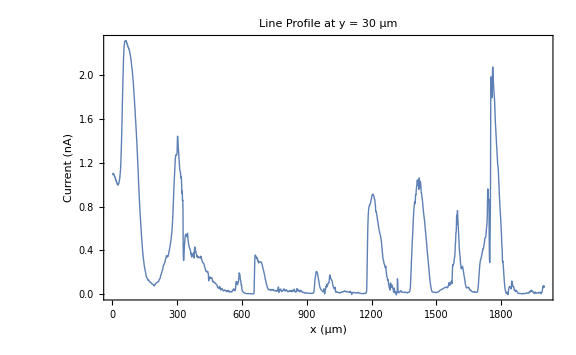

```mathematica
LPy[30]
```

```mathematica
Table[getZ[x,30],{x,1720,1810,1}]
```

{0.444,0.455,0.464,0.475,0.497,0.509,0.515,0.517,0.52,0.523,0.54,0.575,0.6,0.612,0.633,0.66,0.722,0.842,0.96,0.957,0.922,0.883,0.845,0.864,0.749,0.476,0.324,0.29,0.326,0.537,0.729,1.03,1.81,1.98,1.96,1.9,1.84,1.79,1.8,1.91,2.03,2.07,2.05,2.,1.95,1.91,1.86,1.84,1.82,1.79,1.75,1.7,1.64,1.58,1.54,1.51,1.47,1.44,1.4,1.36,1.33,1.29,1.26,1.22,1.19,1.17,1.16,1.13,1.09,1.04,0.997,0.95,0.903,0.854,0.812,0.778,0.751,0.722,0.685,0.642,0.604,0.567,0.528,0.459,0.434,0.405,0.31,0.295,0.302,0.285,0.258}

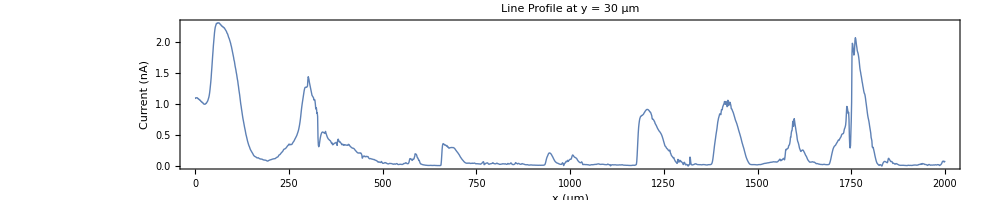

-Graphics-

```mathematica
LPy2[y_]:=Module[{rowIndex,xvals,lineProfile},
rowIndex=Round[y/dy]+1;
If[rowIndex<1||rowIndex>ny,Return["Error: y = "<>ToString[y]<>" µm is out of range."]];
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatrix[[rowIndex]];
ListLinePlot[Transpose[{xvals,lineProfile}],Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm",PlotRange->All,PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->1000,AspectRatio->1/5]];
LPy2[30]
LPy[30]
```

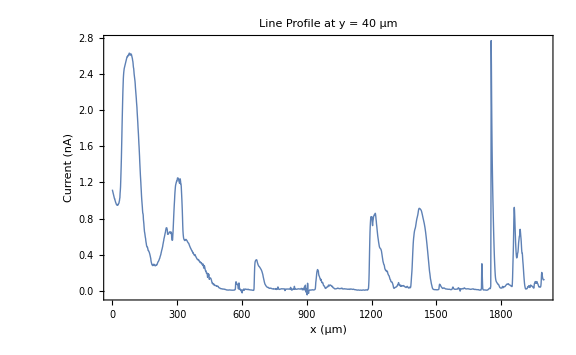

```mathematica
LPy[40]
```

```mathematica
Table[getZ[x,40],{x,1753,1767,1}]
```

{0.978,2.77,2.49,2.13,1.84,1.61,1.42,1.27,1.13,1.01,0.897,0.791,0.691,0.6,0.515}

```mathematica
SmoothZSpike[1753,1767,40]
```

{0.952613,0.975778,0.925963,0.864823,0.891332,0.859434,0.778226,0.721815,0.751053,0.713638,0.6659,0.637511,0.53385,0.540674,0.561383}

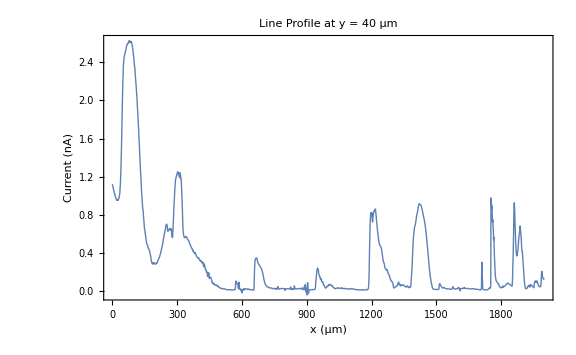

```mathematica
LPy[40]
```

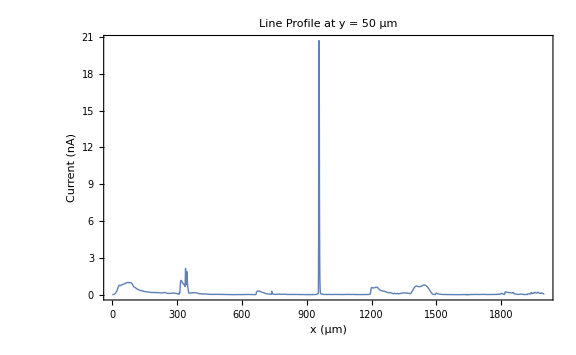

```mathematica
LPy[50]
```

{0.134,3.71,20.7,20.7,19.6,8.56,3.24,1.25,0.513,0.233,0.124,0.0837,0.0685}

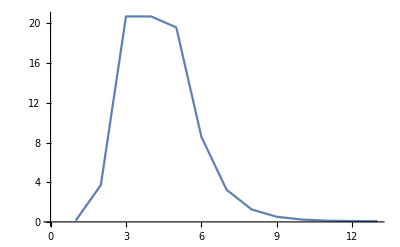

```mathematica
Table[getZ[x,50],{x,954,966,1}]
ListLinePlot[Table[getZ[x,50],{x,954,966,1}]]
```

```mathematica
SmoothZSpike[954,966,50]
```

{0.104697,0.0854405,0.167126,0.0841441,0.130825,0.0739701,0.150315,0.0686074,0.0409364,0.105628,0.10504,0.0886731,0.0863774}

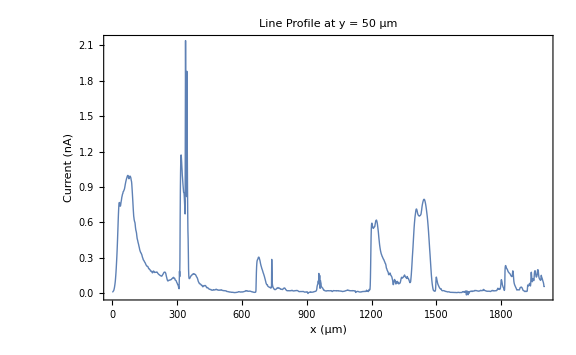

```mathematica
LPy[50]
```

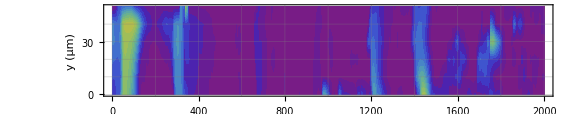

```mathematica
map[zMatrix,0.1,4,20]
```

### c. Correction 2 (optional, need update)

```mathematica
map[zMatrix,0.1,4,20]
```

-Graphics-

```mathematica
{LPy[20],LPy[30],LPy[40]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[getZ[x,30],{x,1730,1800,1}]
```

{0.54,0.575,0.6,0.612,0.633,0.66,0.722,0.842,0.96,0.957,0.922,0.883,0.845,0.864,0.749,0.476,0.324,0.29,0.326,0.537,0.729,1.03,1.81,1.98,1.96,1.9,1.84,1.79,1.8,1.91,2.03,2.07,2.05,2.,1.95,1.91,1.86,1.84,1.82,1.79,1.75,1.7,1.64,1.58,1.54,1.51,1.47,1.44,1.4,1.36,1.33,1.29,1.26,1.22,1.19,1.17,1.16,1.13,1.09,1.04,0.997,0.95,0.903,0.854,0.812,0.778,0.751,0.722,0.685,0.642,0.604}

```mathematica
Table[getZ[x,30],{x,1735,1747,1}]
```

{0.66,0.722,0.842,0.96,0.957,0.922,0.883,0.845,0.864,0.749,0.476,0.324,0.29}

```mathematica
Table[getZ[x,30],{x,1748,1759,1}]
```

{0.326,0.537,0.729,1.03,1.81,1.98,1.96,1.9,1.84,1.79,1.8,1.91}

```mathematica
SmoothZSpike[1735,1747,30]
SmoothZSpike[1748,1759,30]
```

{0.703145,0.654914,0.559953,0.527362,0.574504,0.550119,0.520043,0.484046,0.453086,0.339134,0.32463,0.323315,0.321565}

{0.293841,0.454135,0.629223,0.720145,0.857644,0.99977,1.19685,1.36378,1.44099,1.65163,1.73197,1.95515}

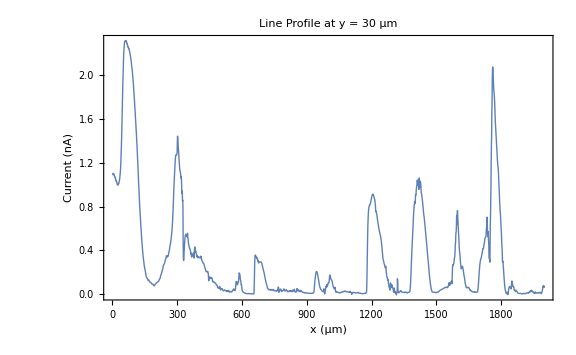

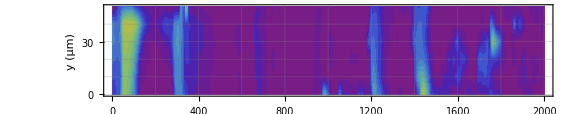

```mathematica
LPy[30]
map[zMatrix,0.1,4,20]
```

```mathematica
LPy[50]
```

-Graphics-

```mathematica
Table[getZ[x,50],{x,300,400,1}]
```

{0.0856,0.0818,0.0755,0.0704,0.0685,0.066,0.0578,0.0471,0.0401,0.0376,0.105,0.185,0.14,0.281,0.616,0.871,1.03,1.13,1.17,1.17,1.14,1.11,1.07,1.04,1.,0.976,0.949,0.923,0.9,0.877,0.854,0.851,0.849,0.821,0.782,0.745,0.708,0.671,1.45,2.14,1.66,1.31,1.09,0.928,0.818,1.88,1.62,1.25,0.912,0.686,0.532,0.46,0.341,0.201,0.147,0.128,0.123,0.123,0.125,0.127,0.13,0.136,0.139,0.142,0.146,0.148,0.149,0.149,0.152,0.155,0.158,0.159,0.16,0.161,0.163,0.164,0.165,0.163,0.161,0.161,0.163,0.161,0.16,0.159,0.158,0.157,0.154,0.15,0.147,0.142,0.138,0.136,0.134,0.13,0.125,0.12,0.114,0.106,0.1,0.0957,0.0925}

```mathematica
Table[getZ[x,50],{x,334,344,1}]
```

{0.782,0.745,0.708,0.671,1.45,2.14,1.66,1.31,1.09,0.928,0.818}

```mathematica
SmoothZSpike[334,344,50]
```

{0.800071,0.753509,0.837532,0.830961,0.774267,0.756094,0.777145,0.80103,0.804482,0.833532,0.817467}

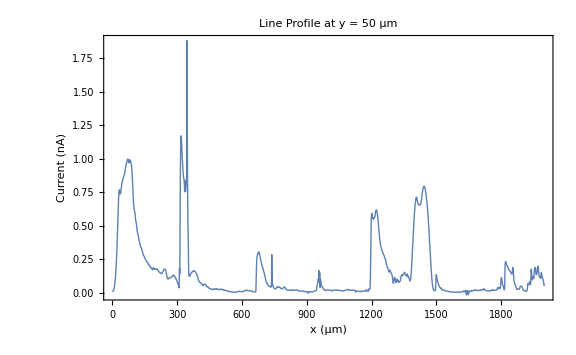

```mathematica
LPy[50]
```

```mathematica
Table[getZ[x,50],{x,341,351,1}]
```

{0.80103,0.804482,0.833532,0.817467,1.88,1.62,1.25,0.912,0.686,0.532,0.46}

```mathematica
SmoothZSpike[341,351,50]
```

{0.840395,0.762747,0.772371,0.657224,0.68048,0.611963,0.63335,0.524009,0.524712,0.515163,0.472781}

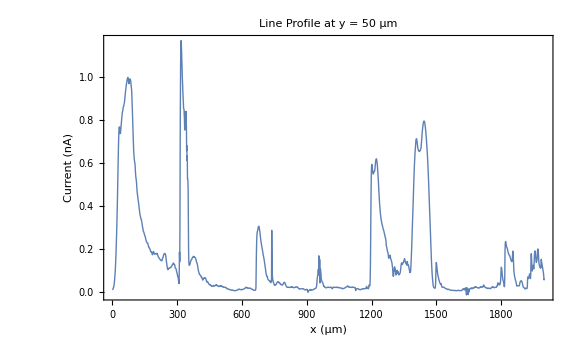

```mathematica
LPy[50]
```

## Final?

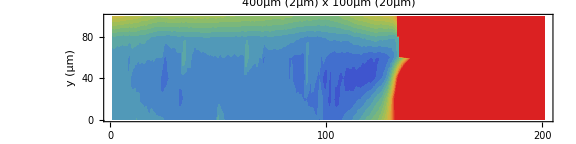

```mathematica
map[zMatrix,0.1,2,20]
```

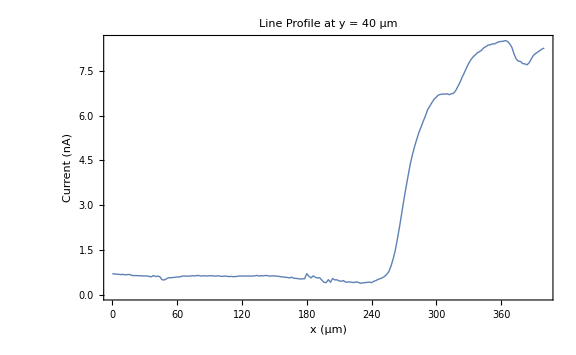

```mathematica
LPy[40]
```

## Final touch-flip

```mathematica
zMatrixR=Map[Reverse,zMatrix];
```

```mathematica
ClearAll[LPy];
LPyR[y_]:=Module[{rowIndex,xvals,lineProfile},
rowIndex=Round[y/dy]+1;
If[rowIndex<1||rowIndex>ny,Return["Error: y = "<>ToString[y]<>" µm is out of range."]];
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatrixR[[rowIndex]];
ListLinePlot[Transpose[{xvals,lineProfile}],Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm",PlotRange->All,PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]];
```

```mathematica
GetLPyRData[y_]:=Module[{rowIndex,xvals,lineProfile},rowIndex=Round[y/dy]+1;
If[rowIndex<1||rowIndex>ny,Return["Error: y = "<>ToString[y]<>" µm is out of range."]];
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatrixR[[rowIndex]];
Transpose[{xvals,lineProfile}]];
```

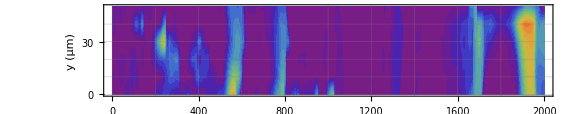

```mathematica
map[zMatrixR,0.1,3,20]
```

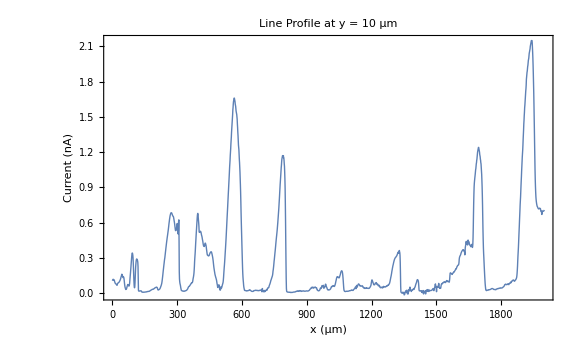

```mathematica
LPyR[10]
```

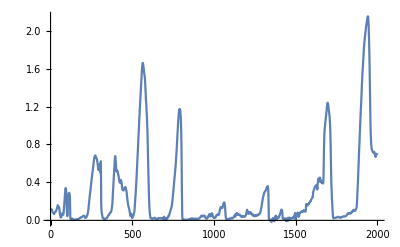

LPyR_10.csv

```mathematica
data10=GetLPyRData[10];
ListLinePlot[data10,PlotRange->All]
Export["LPyR_10.csv",data10]
```

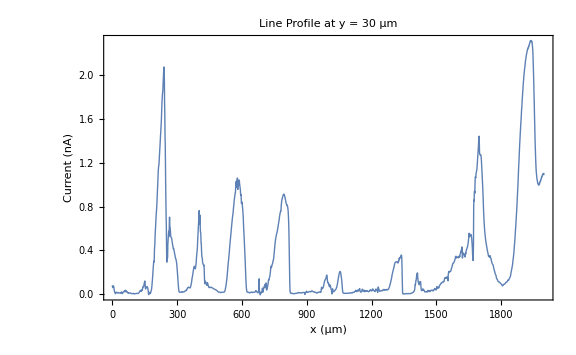

```mathematica
LPyR[30]
```

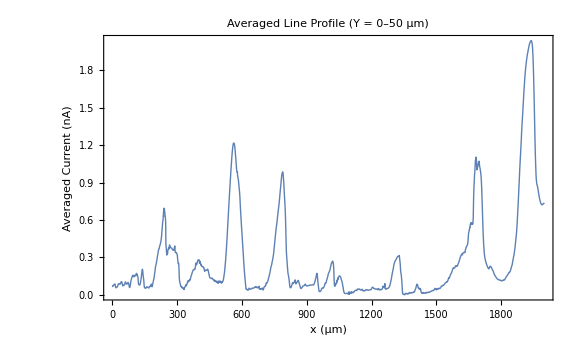

```mathematica
avgProfile=Mean[zMatrixR];
xvals=Range[0,dx*(nx-1),dx];
ListLinePlot[Transpose[{xvals,avgProfile}],PlotRange->All,Frame->True,FrameLabel->{"x (μm)","Averaged Current (nA)"},PlotLabel->"Averaged Line Profile (Y = 0–50 μm)",PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

{2,2001}

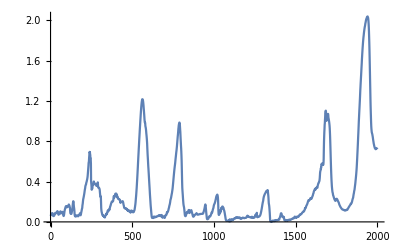

data_avg.csv

```mathematica
xvals//Dimensions;
dataavg={xvals,avgProfile};
dataavg//Dimensions
ListLinePlot[Transpose[dataavg],PlotRange->All]
Export["data_avg.csv",dataavg]
```

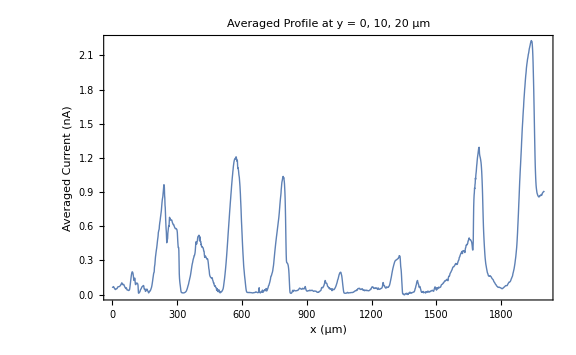

```mathematica
avgProfile2=Mean[zMatrixR[[{2,3,4}]]];
xvals=Range[0,dx*(nx-1),dx];
ListLinePlot[Transpose[{xvals,avgProfile2}],PlotRange->All,Frame->True,FrameLabel->{"x (μm)","Averaged Current (nA)"},PlotLabel->"Averaged Profile at y = 0, 10, 20 μm",PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

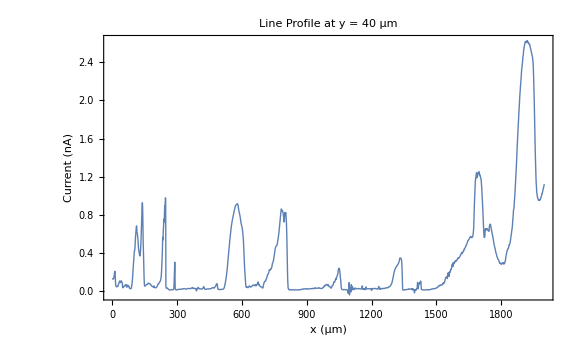

```mathematica
LPyR[40]
```